# MS-C2105: Introduction to Optimization // Week 4

Harri Hakula, 2022

## Routines

```mathematica
IntegerRegionPlot[quantifier_,{xmin_,xmax_},{ymin_,ymax_},rad_:0.5]:=Graphics[Flatten[Table[If[quantifier,{Red,Disk[{Subscript[x, 1],Subscript[x, 2]},rad]},{Blue,Disk[{Subscript[x, 1],Subscript[x, 2]},rad]}],{Subscript[x, 1],xmin,xmax},{Subscript[x, 2],ymin,ymax}]],Frame->True];
```

## Branch and Bound

min  x_1-2 x_2
subject to 
2 x_1+x_2≤5,
-4 x_1+4 x_2≤5, 
x_1,x_2≥0, and x_1, x_2 ∈ ℕ

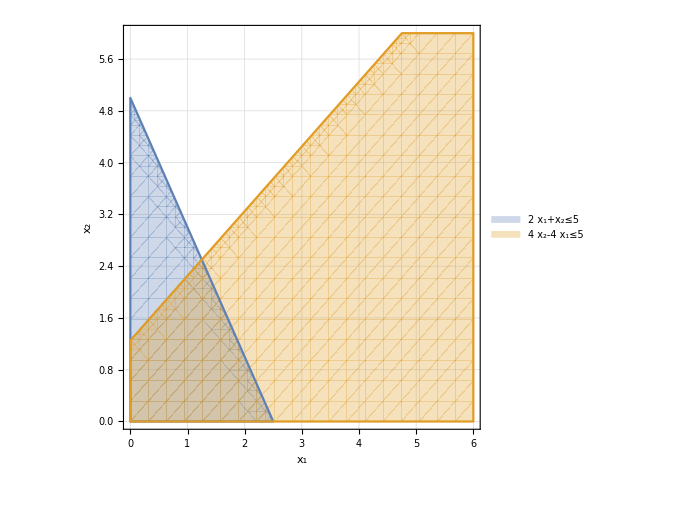

```mathematica
base=RegionPlot[{2 Subscript[x, 1]+Subscript[x, 2]≤5,-4 Subscript[x, 1]+4 Subscript[x, 2]≤5},{Subscript[x, 1],0,6},{Subscript[x, 2],0,6},FrameStyle->Directive[Thick,16],FrameLabel->Automatic,GridLines->Automatic,PlotLegends->{2 Subscript[x, 1]+Subscript[x, 2]≤5,-4 Subscript[x, 1]+4 Subscript[x, 2]≤5}]
```

## Integer View

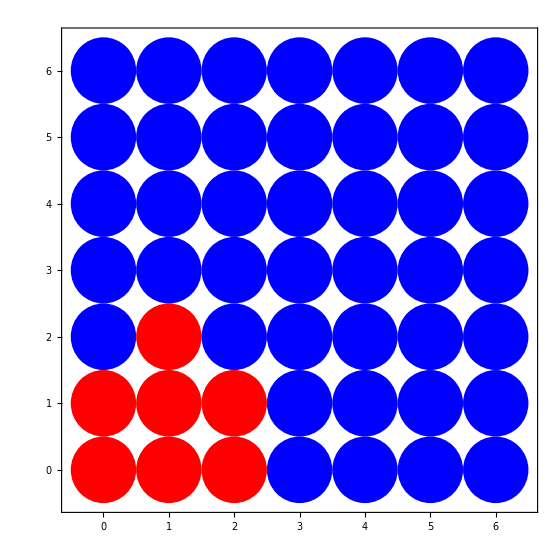

```mathematica
top=IntegerRegionPlot[2 Subscript[x, 1]+Subscript[x, 2]≤5&&-4 Subscript[x, 1]+4 Subscript[x, 2]≤5&&Subscript[x, 1]>=0&&Subscript[x, 2]>=0,{0,6},{0,6}]
```

## Relation to Continuous Problem

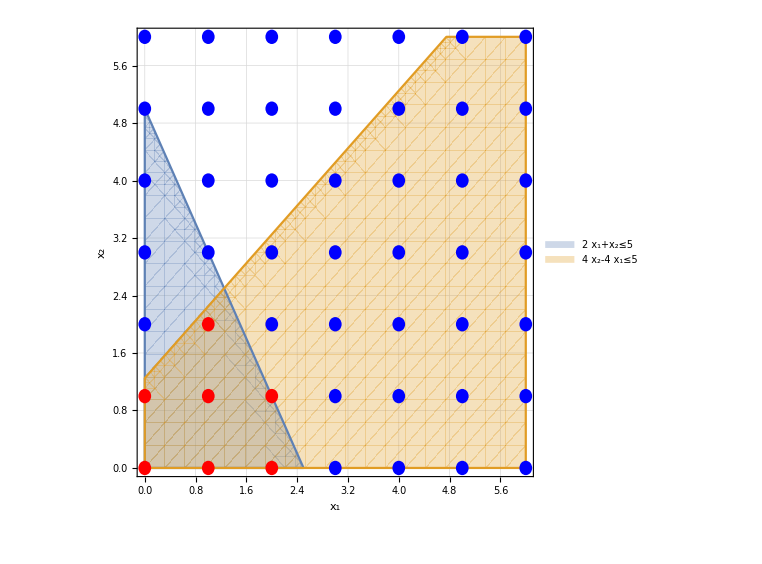

```mathematica
top=IntegerRegionPlot[2 Subscript[x, 1]+Subscript[x, 2]≤5&&-4 Subscript[x, 1]+4 Subscript[x, 2]≤5&&Subscript[x, 1]>=0&&Subscript[x, 2]>=0,{0,6},{0,6},0.1];
Show[base,top]
```

## What' s the Solution Then?

min

```mathematica
({x,y}↦x-2y)@@@{{1,1},{1,2},{2,1},{0,0},{1,0},{2,0},{0,1}}
```

{-1,-3,0,0,1,2,-2}

The solution is x_1=1, x_2=2.

## Return to the 1st Example

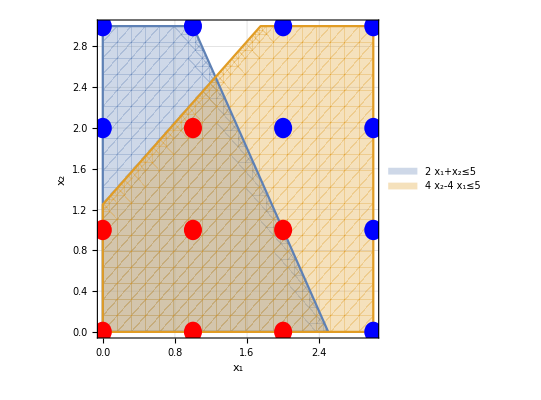

```mathematica
base=RegionPlot[{2 Subscript[x, 1]+Subscript[x, 2]≤5,-4 Subscript[x, 1]+4 Subscript[x, 2]≤5},{Subscript[x, 1],0,3},{Subscript[x, 2],0,3},FrameStyle->Directive[Thick,16],FrameLabel->Automatic,GridLines->Automatic,PlotLegends->{2 Subscript[x, 1]+Subscript[x, 2]≤5,-4 Subscript[x, 1]+4 Subscript[x, 2]≤5}];top=IntegerRegionPlot[2 Subscript[x, 1]+Subscript[x, 2]≤5&&-4 Subscript[x, 1]+4 Subscript[x, 2]≤5&&Subscript[x, 1]>=0&&Subscript[x, 2]>=0,{0,3},{0,3},0.1];
log=Show[base,top]
```

## Feasible Region

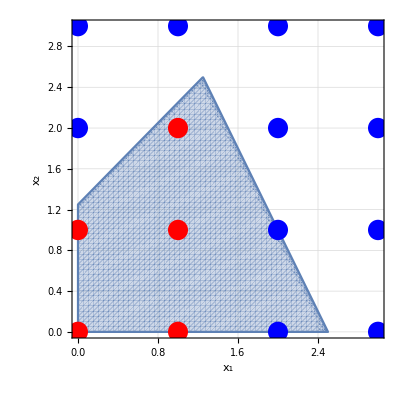

```mathematica
nbase=RegionPlot[{2 Subscript[x, 1]+Subscript[x, 2]≤5&&-4 Subscript[x, 1]+4 Subscript[x, 2]≤5},{Subscript[x, 1],0,3},{Subscript[x, 2],0,3},FrameStyle->Directive[Thick,16],FrameLabel->Automatic,GridLines->Automatic,PlotPoints->60];
Show[nbase,top]
```

## Step 1

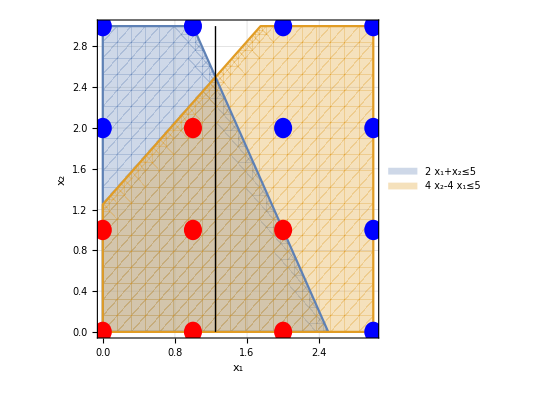

```mathematica
log1=Show[log,Graphics[Line[{{5/4,0},{5/4,3}}]]]
```

## Feasible Region After Constraint

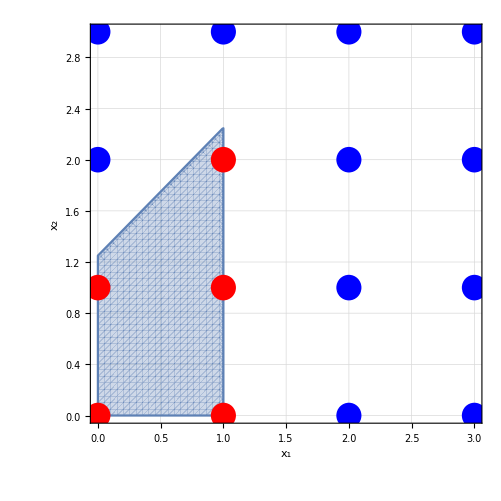

```mathematica
nbase=RegionPlot[{2 Subscript[x, 1]+Subscript[x, 2]≤5&&-4 Subscript[x, 1]+4 Subscript[x, 2]≤5&&Subscript[x, 1]<=1},{Subscript[x, 1],0,3},{Subscript[x, 2],0,3},FrameStyle->Directive[Thick,16],FrameLabel->Automatic,GridLines->Automatic,PlotPoints->60];
Show[nbase,top]
```

## Step 2

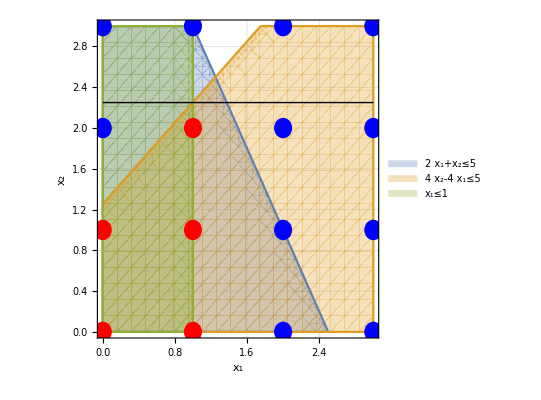

```mathematica
base=RegionPlot[{2 Subscript[x, 1]+Subscript[x, 2]≤5,-4 Subscript[x, 1]+4 Subscript[x, 2]≤5,Subscript[x, 1]<=1},{Subscript[x, 1],0,3},{Subscript[x, 2],0,3},FrameStyle->Directive[Thick,16],FrameLabel->Automatic,GridLines->Automatic,PlotLegends->{2 Subscript[x, 1]+Subscript[x, 2]≤5,-4 Subscript[x, 1]+4 Subscript[x, 2]≤5,Subscript[x, 1]<=1}];top=IntegerRegionPlot[2 Subscript[x, 1]+Subscript[x, 2]≤5&&-4 Subscript[x, 1]+4 Subscript[x, 2]≤5&&1>=Subscript[x, 1]>=0&&Subscript[x, 2]>=0,{0,3},{0,3},0.1];
log=Show[base,top];
log2=Show[log,1Graphics[Line[{{0,9/4},{3,9/4}}]]]
```

## Feasible Region After Second Constraint

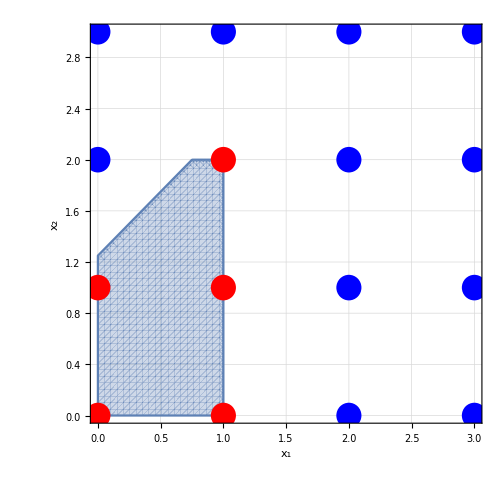

```mathematica
nbase=RegionPlot[{2 Subscript[x, 1]+Subscript[x, 2]≤5&&-4 Subscript[x, 1]+4 Subscript[x, 2]≤5&&Subscript[x, 1]<=1&&Subscript[x, 2]<=2},{Subscript[x, 1],0,3},{Subscript[x, 2],0,3},FrameStyle->Directive[Thick,16],FrameLabel->Automatic,GridLines->Automatic,PlotPoints->60];
Show[nbase,top]
```

## Step 3

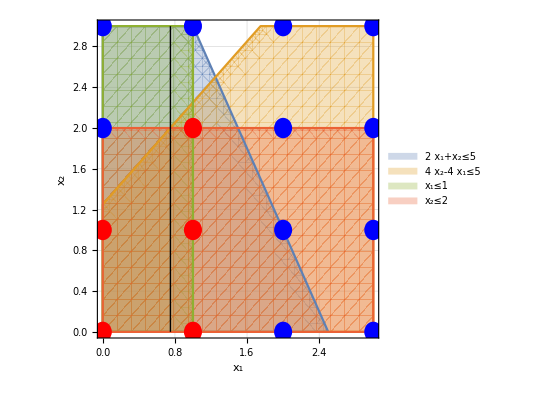

```mathematica
base=RegionPlot[{2 Subscript[x, 1]+Subscript[x, 2]≤5,-4 Subscript[x, 1]+4 Subscript[x, 2]≤5,Subscript[x, 1]<=1,Subscript[x, 2]<=2},{Subscript[x, 1],0,3},{Subscript[x, 2],0,3},FrameStyle->Directive[Thick,16],FrameLabel->Automatic,GridLines->Automatic,PlotLegends->{2 Subscript[x, 1]+Subscript[x, 2]≤5,-4 Subscript[x, 1]+4 Subscript[x, 2]≤5,Subscript[x, 1]<=1,Subscript[x, 2]<=2}];top=IntegerRegionPlot[2 Subscript[x, 1]+Subscript[x, 2]≤5&&-4 Subscript[x, 1]+4 Subscript[x, 2]≤5&&1>=Subscript[x, 1]>=0&&2>=Subscript[x, 2]>=0,{0,3},{0,3},0.1];
log=Show[base,top];
log2=Show[log,1Graphics[Line[{{3/4,0},{3/4,3}}]]]
```

## Final Feasible Region

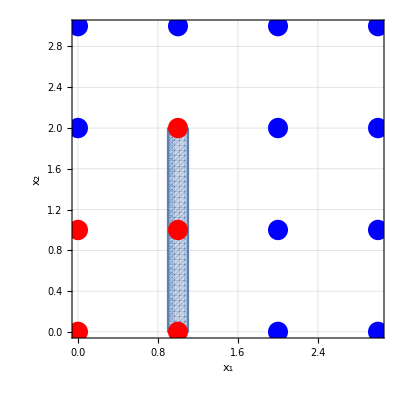

```mathematica
nbase=RegionPlot[{2 Subscript[x, 1]+Subscript[x, 2]≤5&&-4 Subscript[x, 1]+4 Subscript[x, 2]≤5&&1.1>=Subscript[x, 1]>=0.9&&Subscript[x, 2]<=2},{Subscript[x, 1],0,3},{Subscript[x, 2],0,3},FrameStyle->Directive[Thick,16],FrameLabel->Automatic,GridLines->Automatic,PlotPoints->60];
Show[nbase,top]
```